## Simplified FK of SRSPM

```mathematica
SetDirectory[NotebookDirectory[]]
(*<<ed5314utils_en.m*)
```

/home/nightmareforev/git/root_tracking/Mathematica/SRSPM/FK

```mathematica
rotZ[θ_]:={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}};
```

```mathematica
(*fixed platform*)
b1 = {1, 0, 0};
b2 = rotZ[2*0.2985].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
tempa = Table[Symbol["b"<>ToString[i]],{i, 6}];
b = Table[rotZ[(2π/3-2*0.2985)/2].tempa[[i]],{i, Length[tempa]}];
ashift=b-{b[[1]],b[[1]],b[[1]],b[[1]],b[[1]],b[[1]]}
```

{{0.,0.,0.},{-0.509373,0.294087,0.},{-1.68835,-0.386598,0.},{-1.68835,-0.974772,0.},{-0.509373,-1.65546,0.},{-2.22045×10^-16,-1.36137,0.}}

```mathematica
(*moving platform*)
a1 = {0.5803, 0, 0};
a2 = rotZ[2*0.6573].a1;
a3 = rotZ[2π/3].a1;
a4 = rotZ[2π/3].a2;
a5 = rotZ[4π/3].a1;
a6 = rotZ[4π/3].a2;
tempa = Table[Symbol["a"<>ToString[i]],{i, 6}];
a = Table[rotZ[(2π/3-2*0.6573)/2].tempa[[i]],{i, Length[tempa]}];
ashift=a-{a[[1]],a[[1]],a[[1]],a[[1]],a[[1]],a[[1]]}
```

{{0.,0.,0.},{-0.614103,0.354553,0.},{-0.996139,0.133984,0.},{-0.996139,-0.575121,0.},{-0.614103,-0.795689,0.},{-1.11022×10^-16,-0.441137,0.}}

```mathematica
(*lvals for circle tracking example*)
```

```mathematica
(*lvals = {1.4458208723874426,1.568679047566447,1.57865471573012,1.3393859531342835,1.152479064455009,1.286875291086054}*)
```

```mathematica
(*lvals for singularity example*)
```

```mathematica
lvals = {1.5606305002994023,1.5251471621309471,1.3150462596882393,1.1300948138280011,1.1268160733797703,1.5034746579174754}
```

{1.56063,1.52515,1.31505,1.13009,1.12682,1.50347}

```mathematica
l = {l1, l2, l3, l4, l5, l6}
```

{l1,l2,l3,l4,l5,l6}

```mathematica
sub={b2x->-0.5093734006873172,b2y->0.2940868700048578,b2z->0,b3x->-1.6883547421176872,b3y->-0.3865983248395124,b3z->0,b4x->-1.6883547421176874,b4y->-0.9747720648492277,b4z->0,b5x->-0.5093734006873175,b5y->-1.6554572596935981,b5z->0,b6x->-2.220446049250313*10^-16,b6y->-1.3613703896887406,b6z->0,t2x->-0.6141031970306339,t2y->0.35455264611584647,t2z->0,t3x->-0.9961387846155708,t3y->0.13398429678366627,t3z->0,t4x->-0.996138784615571,t4y->-0.5751209954480264,t4z->0,t5x->-0.6141031970306341,t5y->-0.7956893447802065,t5z->0,t6x->-1.1102230246251565*10^-16,t6y->-0.44113669866436034,t6z->0}
len={l1->1.4458208723874426,l2->1.568679047566447,l3->1.5786547157301198,l4->1.3393859531342835,l5->1.152479064455009,l6->1.286875291086054}
```

{b2x→-0.509373,b2y→0.294087,b2z→0,b3x→-1.68835,b3y→-0.386598,b3z→0,b4x→-1.68835,b4y→-0.974772,b4z→0,b5x→-0.509373,b5y→-1.65546,b5z→0,b6x→-2.22045×10^-16,b6y→-1.36137,b6z→0,t2x→-0.614103,t2y→0.354553,t2z→0,t3x→-0.996139,t3y→0.133984,t3z→0,t4x→-0.996139,t4y→-0.575121,t4z→0,t5x→-0.614103,t5y→-0.795689,t5z→0,t6x→-1.11022×10^-16,t6y→-0.441137,t6z→0}

{l1→1.44582,l2→1.56868,l3→1.57865,l4→1.33939,l5→1.15248,l6→1.28688}

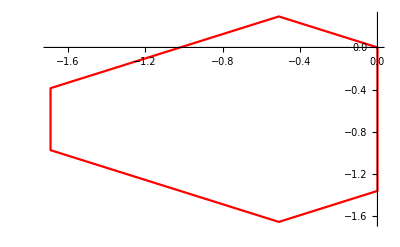

```mathematica
(*Fixed Platform*)
o1={0,0,0};
o2={b2x,b2y,b2z};
o3={b3x,b3y,b3z};
o4={b4x,b4y,b4z};
o5={b5x,b5y,b5z};
o6={b6x,b6y,b6z};
o={o1,o2,o3,o4,o5,o6,o1};
ListLinePlot[(o/.sub)[[;;, 1;;2]],PlotStyle->Red]
(*oj={bjx,bjy,bjz};*)
```

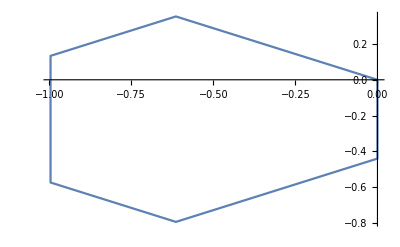

```mathematica
(*Moving platform*)
p1={0,0,0};
p2={t2x,t2y,t2z};
p3={t3x,t3y,t3z};
p4={t4x,t4y,t4z};
p5={t5x,t5y,t5z};
p6={t6x,t6y,t6z};
p={p1,p2,p3,p4,p5,p6,p1};
ListLinePlot[(p/.sub)[[;;, 1;;2]]]
(*pj={tjx,tjy,tjz};*)
```

```mathematica
Cmat={{0,-c3,c2},{c3,0,-c1},{-c2,c1,0}}
```

{{0,-c3,c2},{c3,0,-c1},{-c2,c1,0}}

```mathematica
Rmat=Simplify[(IdentityMatrix[3]+Cmat).Inverse[(IdentityMatrix[3]-Cmat)]];
```

```mathematica
xvec={x,y,z};
```

```mathematica
p1o=xvec+Rmat.p1;
p2o=xvec+Rmat.p2;
p3o=xvec+Rmat.p3;
p4o=xvec+Rmat.p4;
p5o=xvec+Rmat.p5;
p6o=xvec+Rmat.p6;
(*pjo=xvec+Rmat.pj;*)
```

```mathematica
eq1=(p1o-o1).(p1o-o1)-l1^2
```

-l1^2+x^2+y^2+z^2

```mathematica
(*monoprod[{a_,b_}]:=a.b;
eqj=FullSimplify[monoprod[FullSimplify[monopoly[Factor[(pjo-oj).(pjo-oj)-lj^2][[3]],{bjx,bjy,bjz,tjx,tjy,tjz,lj}]]/.{ (x^2+y^2+z^2)-> w,1+c1^2+c2^2+c3^2-> c0,-1-c1^2-c2^2-c3^2-> -c0}]];*)
```

```mathematica
eq2=FullSimplify[Factor[(p2o-o2).(p2o-o2)-l2^2][[3]]];
eq3=FullSimplify[Factor[(p3o-o3).(p3o-o3)-l3^2][[3]]];
eq4=FullSimplify[Factor[(p4o-o4).(p4o-o4)-l4^2][[3]]];
eq5=FullSimplify[Factor[(p5o-o5).(p5o-o5)-l5^2][[3]]];
eq6=FullSimplify[Factor[(p6o-o6).(p6o-o6)-l6^2][[3]]];
```

```mathematica
nsol=Timing[NSolve[N[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len),50]=={0,0,0,0,0,0},{x,y,z,c1,c2,c3},Method-> "HomotopyContinuation"]];
```

```mathematica
nsol[[2]]//Chop
```

{{x→-2.28056×10^17-7.28995×10^17 ⅈ,y→7.26736×10^17-2.2371×10^17 ⅈ,z→-6.62991×10^16+5.54034×10^16 ⅈ,c1→-0.867903+0.677306 ⅈ,c2→-0.626987-0.762563 ⅈ,c3→0.103817+1.05684 ⅈ},{x→-2.28056×10^17+7.28995×10^17 ⅈ,y→7.26736×10^17+2.2371×10^17 ⅈ,z→-6.62991×10^16-5.54034×10^16 ⅈ,c1→-0.867903-0.677306 ⅈ,c2→-0.626987+0.762563 ⅈ,c3→0.103817-1.05684 ⅈ},{x→-2.28056×10^17-7.28995×10^17 ⅈ,y→7.26736×10^17-2.2371×10^17 ⅈ,z→-6.62991×10^16+5.54034×10^16 ⅈ,c1→0.772379-0.517395 ⅈ,c2→0.554854+0.875733 ⅈ,c3→-0.0920629+0.937177 ⅈ},{x→-2.28056×10^17+7.28995×10^17 ⅈ,y→7.26736×10^17+2.2371×10^17 ⅈ,z→-6.62991×10^16-5.54034×10^16 ⅈ,c1→0.772379+0.517395 ⅈ,c2→0.554854-0.875733 ⅈ,c3→-0.0920629-0.937177 ⅈ},{x→-2.28056×10^17-7.28995×10^17 ⅈ,y→7.26736×10^17-2.2371×10^17 ⅈ,z→-6.62991×10^16+5.54034×10^16 ⅈ,c1→0.772379-0.517395 ⅈ,c2→0.554854+0.875733 ⅈ,c3→-0.0920629+0.937177 ⅈ},{x→-2.28056×10^17+7.28995×10^17 ⅈ,y→7.26736×10^17+2.2371×10^17 ⅈ,z→-6.62991×10^16-5.54034×10^16 ⅈ,c1→0.772379+0.517395 ⅈ,c2→0.554854-0.875733 ⅈ,c3→-0.0920629-0.937177 ⅈ},{x→-2.28056×10^17-7.28995×10^17 ⅈ,y→7.26736×10^17-2.2371×10^17 ⅈ,z→-6.62991×10^16+5.54034×10^16 ⅈ,c1→-0.867903+0.677306 ⅈ,c2→-0.626987-0.762563 ⅈ,c3→0.103817+1.05684 ⅈ},{x→-2.28056×10^17+7.28995×10^17 ⅈ,y→7.26736×10^17+2.2371×10^17 ⅈ,z→-6.62991×10^16-5.54034×10^16 ⅈ,c1→-0.867903-0.677306 ⅈ,c2→-0.626987+0.762563 ⅈ,c3→0.103817-1.05684 ⅈ},{x→-2.28056×10^17-7.28995×10^17 ⅈ,y→7.26736×10^17-2.2371×10^17 ⅈ,z→6.62991×10^16-5.54034×10^16 ⅈ,c1→0.867903-0.677306 ⅈ,c2→0.626987+0.762563 ⅈ,c3→0.103817+1.05684 ⅈ},{x→-2.28056×10^17+7.28995×10^17 ⅈ,y→7.26736×10^17+2.2371×10^17 ⅈ,z→6.62991×10^16+5.54034×10^16 ⅈ,c1→0.867903+0.677306 ⅈ,c2→0.626987-0.762563 ⅈ,c3→0.103817-1.05684 ⅈ},{x→-2.28056×10^17-7.28995×10^17 ⅈ,y→7.26736×10^17-2.2371×10^17 ⅈ,z→6.62991×10^16-5.54034×10^16 ⅈ,c1→-0.772379+0.517395 ⅈ,c2→-0.554854-0.875733 ⅈ,c3→-0.0920629+0.937177 ⅈ},{x→-2.28056×10^17+7.28995×10^17 ⅈ,y→7.26736×10^17+2.2371×10^17 ⅈ,z→6.62991×10^16+5.54034×10^16 ⅈ,c1→-0.772379-0.517395 ⅈ,c2→-0.554854+0.875733 ⅈ,c3→-0.0920629-0.937177 ⅈ},{x→-2.28056×10^17-7.28995×10^17 ⅈ,y→7.26736×10^17-2.2371×10^17 ⅈ,z→6.62991×10^16-5.54034×10^16 ⅈ,c1→-0.772379+0.517395 ⅈ,c2→-0.554854-0.875733 ⅈ,c3→-0.0920629+0.937177 ⅈ},{x→-2.28056×10^17+7.28995×10^17 ⅈ,y→7.26736×10^17+2.2371×10^17 ⅈ,z→6.62991×10^16+5.54034×10^16 ⅈ,c1→-0.772379-0.517395 ⅈ,c2→-0.554854+0.875733 ⅈ,c3→-0.0920629-0.937177 ⅈ},{x→-2.28056×10^17-7.28995×10^17 ⅈ,y→7.26736×10^17-2.2371×10^17 ⅈ,z→6.62991×10^16-5.54034×10^16 ⅈ,c1→0.867903-0.677306 ⅈ,c2→0.626987+0.762563 ⅈ,c3→0.103817+1.05684 ⅈ},{x→-2.28056×10^17+7.28995×10^17 ⅈ,y→7.26736×10^17+2.2371×10^17 ⅈ,z→6.62991×10^16+5.54034×10^16 ⅈ,c1→0.867903+0.677306 ⅈ,c2→0.626987-0.762563 ⅈ,c3→0.103817-1.05684 ⅈ},{x→5.95779×10^16,y→-1.7185×10^16,z→0.-6.20069×10^16 ⅈ,c1→0.-0.886381 ⅈ,c2→0.+1.29644 ⅈ,c3→-1.21096},{x→5.95779×10^16,y→-1.7185×10^16,z→0.+6.20069×10^16 ⅈ,c1→0.+0.886381 ⅈ,c2→0.-1.29644 ⅈ,c3→-1.21096},{x→5.95779×10^16,y→-1.7185×10^16,z→0.-6.20069×10^16 ⅈ,c1→0.+1.07059 ⅈ,c2→0.+0.731963 ⅈ,c3→0.825788},{x→5.95779×10^16,y→-1.7185×10^16,z→0.+6.20069×10^16 ⅈ,c1→0.-1.07059 ⅈ,c2→0.-0.731963 ⅈ,c3→0.825788},{x→5.95779×10^16,y→-1.7185×10^16,z→0.-6.20069×10^16 ⅈ,c1→0.+1.07059 ⅈ,c2→0.+0.731963 ⅈ,c3→0.825788},{x→5.95779×10^16,y→-1.7185×10^16,z→0.+6.20069×10^16 ⅈ,c1→0.-1.07059 ⅈ,c2→0.-0.731963 ⅈ,c3→0.825788},{x→5.95779×10^16,y→-1.7185×10^16,z→0.-6.20069×10^16 ⅈ,c1→0.-0.886381 ⅈ,c2→0.+1.29644 ⅈ,c3→-1.21096},{x→5.95779×10^16,y→-1.7185×10^16,z→0.+6.20069×10^16 ⅈ,c1→0.+0.886381 ⅈ,c2→0.-1.29644 ⅈ,c3→-1.21096},{x→-3.23874×10^16+1.65248×10^16 ⅈ,y→1.60297×10^16+2.17673×10^16 ⅈ,z→-7.5089×10^15-2.48071×10^16 ⅈ,c1→0.883719-0.223616 ⅈ,c2→-0.144519-1.32295 ⅈ,c3→-0.0751884-0.0854156 ⅈ},{x→-3.23874×10^16-1.65248×10^16 ⅈ,y→1.60297×10^16-2.17673×10^16 ⅈ,z→-7.5089×10^15+2.48071×10^16 ⅈ,c1→0.883719+0.223616 ⅈ,c2→-0.144519+1.32295 ⅈ,c3→-0.0751884+0.0854156 ⅈ},{x→-3.23874×10^16+1.65248×10^16 ⅈ,y→1.60297×10^16+2.17673×10^16 ⅈ,z→-7.5089×10^15-2.48071×10^16 ⅈ,c1→-9.56565-6.72836 ⅈ,c2→-3.65624+7.12764 ⅈ,c3→5.80645-6.59625 ⅈ},{x→-3.23874×10^16-1.65248×10^16 ⅈ,y→1.60297×10^16-2.17673×10^16 ⅈ,z→-7.5089×10^15+2.48071×10^16 ⅈ,c1→-9.56565+6.72836 ⅈ,c2→-3.65624-7.12764 ⅈ,c3→5.80645+6.59625 ⅈ},{x→-3.23874×10^16+1.65248×10^16 ⅈ,y→1.60297×10^16+2.17673×10^16 ⅈ,z→-7.5089×10^15-2.48071×10^16 ⅈ,c1→-9.56565-6.72836 ⅈ,c2→-3.65624+7.12765 ⅈ,c3→5.80645-6.59625 ⅈ},{x→-3.23874×10^16-1.65248×10^16 ⅈ,y→1.60297×10^16-2.17673×10^16 ⅈ,z→-7.5089×10^15+2.48071×10^16 ⅈ,c1→-9.56565+6.72836 ⅈ,c2→-3.65624-7.12765 ⅈ,c3→5.80645+6.59625 ⅈ},{x→-3.23874×10^16+1.65248×10^16 ⅈ,y→1.60297×10^16+2.17673×10^16 ⅈ,z→-7.5089×10^15-2.48071×10^16 ⅈ,c1→0.883719-0.223616 ⅈ,c2→-0.144519-1.32295 ⅈ,c3→-0.0751884-0.0854156 ⅈ},{x→-3.23874×10^16-1.65248×10^16 ⅈ,y→1.60297×10^16-2.17673×10^16 ⅈ,z→-7.5089×10^15+2.48071×10^16 ⅈ,c1→0.883719+0.223616 ⅈ,c2→-0.144519+1.32295 ⅈ,c3→-0.0751884+0.0854156 ⅈ},{x→4.25719×10^16,y→1.5352×10^16,z→0.-4.52554×10^16 ⅈ,c1→0.+1.23407 ⅈ,c2→0.+1.50806 ⅈ,c3→1.67247},{x→4.25719×10^16,y→1.5352×10^16,z→0.+4.52554×10^16 ⅈ,c1→0.-1.23407 ⅈ,c2→0.-1.50806 ⅈ,c3→1.67247},{x→4.25719×10^16,y→1.5352×10^16,z→0.-4.52554×10^16 ⅈ,c1→0.-0.901693 ⅈ,c2→0.+0.737872 ⅈ,c3→-0.597917},{x→4.25719×10^16,y→1.5352×10^16,z→0.+4.52554×10^16 ⅈ,c1→0.+0.901693 ⅈ,c2→0.-0.737872 ⅈ,c3→-0.597917},{x→4.25719×10^16,y→1.5352×10^16,z→0.-4.52554×10^16 ⅈ,c1→0.-0.901693 ⅈ,c2→0.+0.737872 ⅈ,c3→-0.597917},{x→4.25719×10^16,y→1.5352×10^16,z→0.+4.52554×10^16 ⅈ,c1→0.+0.901693 ⅈ,c2→0.-0.737872 ⅈ,c3→-0.597917},{x→4.25719×10^16,y→1.5352×10^16,z→0.-4.52554×10^16 ⅈ,c1→0.+1.23407 ⅈ,c2→0.+1.50806 ⅈ,c3→1.67247},{x→4.25719×10^16,y→1.5352×10^16,z→0.+4.52554×10^16 ⅈ,c1→0.-1.23407 ⅈ,c2→0.-1.50806 ⅈ,c3→1.67247},{x→-3.23874×10^16-1.65248×10^16 ⅈ,y→1.60297×10^16-2.17673×10^16 ⅈ,z→7.5089×10^15-2.48071×10^16 ⅈ,c1→-0.883719-0.223616 ⅈ,c2→0.144519-1.32295 ⅈ,c3→-0.0751884+0.0854156 ⅈ},{x→-3.23874×10^16+1.65248×10^16 ⅈ,y→1.60297×10^16+2.17673×10^16 ⅈ,z→7.5089×10^15+2.48071×10^16 ⅈ,c1→-0.883719+0.223616 ⅈ,c2→0.144519+1.32295 ⅈ,c3→-0.0751884-0.0854156 ⅈ},{x→-3.23874×10^16-1.65248×10^16 ⅈ,y→1.60297×10^16-2.17673×10^16 ⅈ,z→7.5089×10^15-2.48071×10^16 ⅈ,c1→9.56565-6.72836 ⅈ,c2→3.65624+7.12764 ⅈ,c3→5.80645+6.59625 ⅈ},{x→-3.23874×10^16+1.65248×10^16 ⅈ,y→1.60297×10^16+2.17673×10^16 ⅈ,z→7.5089×10^15+2.48071×10^16 ⅈ,c1→9.56565+6.72836 ⅈ,c2→3.65624-7.12764 ⅈ,c3→5.80645-6.59625 ⅈ},{x→-3.23874×10^16-1.65248×10^16 ⅈ,y→1.60297×10^16-2.17673×10^16 ⅈ,z→7.5089×10^15-2.48071×10^16 ⅈ,c1→9.56565-6.72836 ⅈ,c2→3.65624+7.12765 ⅈ,c3→5.80645+6.59625 ⅈ},{x→-3.23874×10^16+1.65248×10^16 ⅈ,y→1.60297×10^16+2.17673×10^16 ⅈ,z→7.5089×10^15+2.48071×10^16 ⅈ,c1→9.56565+6.72836 ⅈ,c2→3.65624-7.12765 ⅈ,c3→5.80645-6.59625 ⅈ},{x→-3.23874×10^16-1.65248×10^16 ⅈ,y→1.60297×10^16-2.17673×10^16 ⅈ,z→7.5089×10^15-2.48071×10^16 ⅈ,c1→-0.883719-0.223616 ⅈ,c2→0.144519-1.32295 ⅈ,c3→-0.0751884+0.0854156 ⅈ},{x→-3.23874×10^16+1.65248×10^16 ⅈ,y→1.60297×10^16+2.17673×10^16 ⅈ,z→7.5089×10^15+2.48071×10^16 ⅈ,c1→-0.883719+0.223616 ⅈ,c2→0.144519+1.32295 ⅈ,c3→-0.0751884-0.0854156 ⅈ},{x→-4.91531×10^15,y→1.47005×10^16,z→0.-1.55005×10^16 ⅈ,c1→0.+0.0741345 ⅈ,c2→0.-3.37523 ⅈ,c3→-3.22454},{x→-4.91531×10^15,y→1.47005×10^16,z→0.+1.55005×10^16 ⅈ,c1→0.-0.0741345 ⅈ,c2→0.+3.37523 ⅈ,c3→-3.22454},{x→-4.91531×10^15,y→1.47005×10^16,z→0.-1.55005×10^16 ⅈ,c1→0.-1.04673 ⅈ,c2→0.-0.0229907 ⅈ,c3→0.310122},{x→-4.91531×10^15,y→1.47005×10^16,z→0.+1.55005×10^16 ⅈ,c1→0.+1.04673 ⅈ,c2→0.+0.0229907 ⅈ,c3→0.310122},{x→-4.91531×10^15,y→1.47005×10^16,z→0.-1.55005×10^16 ⅈ,c1→0.-1.04673 ⅈ,c2→0.-0.0229907 ⅈ,c3→0.310122},{x→-4.91531×10^15,y→1.47005×10^16,z→0.+1.55005×10^16 ⅈ,c1→0.+1.04673 ⅈ,c2→0.+0.0229907 ⅈ,c3→0.310122},{x→-4.91531×10^15,y→1.47005×10^16,z→0.-1.55005×10^16 ⅈ,c1→0.+0.0741344 ⅈ,c2→0.-3.37523 ⅈ,c3→-3.22454},{x→-4.91531×10^15,y→1.47005×10^16,z→0.+1.55005×10^16 ⅈ,c1→0.-0.0741344 ⅈ,c2→0.+3.37523 ⅈ,c3→-3.22454},{x→-1.0093×10^16+1.05133×10^15 ⅈ,y→-3.08387×10^15+5.52478×10^15 ⅈ,z→-2.94072×10^15-9.40206×10^15 ⅈ,c1→-1.15637+1.22693 ⅈ,c2→0.018763+0.0782776 ⅈ,c3→-1.03113-1.37452 ⅈ},{x→-1.0093×10^16-1.05133×10^15 ⅈ,y→-3.08387×10^15-5.52478×10^15 ⅈ,z→-2.94072×10^15+9.40206×10^15 ⅈ,c1→-1.15637-1.22693 ⅈ,c2→0.018763-0.0782776 ⅈ,c3→-1.03113+1.37452 ⅈ},{x→-1.0093×10^16+1.05133×10^15 ⅈ,y→-3.08387×10^15+5.52478×10^15 ⅈ,z→-2.94072×10^15-9.40206×10^15 ⅈ,c1→0.0429939+0.0186024 ⅈ,c2→-0.167334-0.966821 ⅈ,c3→0.349235-0.465538 ⅈ},{x→-1.0093×10^16-1.05133×10^15 ⅈ,y→-3.08387×10^15-5.52478×10^15 ⅈ,z→-2.94072×10^15+9.40206×10^15 ⅈ,c1→0.0429939-0.0186024 ⅈ,c2→-0.167334+0.966821 ⅈ,c3→0.349235+0.465538 ⅈ},{x→-1.0093×10^16+1.05133×10^15 ⅈ,y→-3.08387×10^15+5.52478×10^15 ⅈ,z→-2.94072×10^15-9.40206×10^15 ⅈ,c1→0.0429939+0.0186024 ⅈ,c2→-0.167334-0.966821 ⅈ,c3→0.349235-0.465538 ⅈ},{x→-1.0093×10^16-1.05133×10^15 ⅈ,y→-3.08387×10^15-5.52478×10^15 ⅈ,z→-2.94072×10^15+9.40206×10^15 ⅈ,c1→0.0429939-0.0186024 ⅈ,c2→-0.167334+0.966821 ⅈ,c3→0.349235+0.465538 ⅈ},{x→-1.0093×10^16+1.05133×10^15 ⅈ,y→-3.08387×10^15+5.52478×10^15 ⅈ,z→-2.94072×10^15-9.40206×10^15 ⅈ,c1→-1.15637+1.22693 ⅈ,c2→0.018763+0.0782776 ⅈ,c3→-1.03113-1.37452 ⅈ},{x→-1.0093×10^16-1.05133×10^15 ⅈ,y→-3.08387×10^15-5.52478×10^15 ⅈ,z→-2.94072×10^15+9.40206×10^15 ⅈ,c1→-1.15637-1.22693 ⅈ,c2→0.018763-0.0782776 ⅈ,c3→-1.03113+1.37452 ⅈ},{x→7.73221×10^15-2.17252×10^15 ⅈ,y→-4.66483×10^15-7.831×10^15 ⅈ,z→3.66718×10^15-5.38067×10^15 ⅈ,c1→0.0216844+0.0691994 ⅈ,c2→-0.551365+0.477251 ⅈ,c3→-0.245872-1.06413 ⅈ},{x→7.73221×10^15+2.17252×10^15 ⅈ,y→-4.66483×10^15+7.831×10^15 ⅈ,z→3.66718×10^15+5.38067×10^15 ⅈ,c1→0.0216844-0.0691994 ⅈ,c2→-0.551365-0.477251 ⅈ,c3→-0.245872+1.06413 ⅈ},{x→7.73221×10^15-2.17252×10^15 ⅈ,y→-4.66483×10^15-7.831×10^15 ⅈ,z→3.66718×10^15-5.38067×10^15 ⅈ,c1→0.31211+0.590252 ⅈ,c2→-0.0662032+0.00508111 ⅈ,c3→0.206126-0.89211 ⅈ},{x→7.73221×10^15+2.17252×10^15 ⅈ,y→-4.66483×10^15+7.831×10^15 ⅈ,z→3.66718×10^15+5.38067×10^15 ⅈ,c1→0.31211-0.590252 ⅈ,c2→-0.0662032-0.00508111 ⅈ,c3→0.206126+0.89211 ⅈ},{x→7.73221×10^15-2.17252×10^15 ⅈ,y→-4.66483×10^15-7.831×10^15 ⅈ,z→3.66718×10^15-5.38067×10^15 ⅈ,c1→0.31211+0.590252 ⅈ,c2→-0.0662032+0.00508112 ⅈ,c3→0.206126-0.89211 ⅈ},{x→7.73221×10^15+2.17252×10^15 ⅈ,y→-4.66483×10^15+7.831×10^15 ⅈ,z→3.66718×10^15+5.38067×10^15 ⅈ,c1→0.31211-0.590252 ⅈ,c2→-0.0662032-0.00508112 ⅈ,c3→0.206126+0.89211 ⅈ},{x→7.73221×10^15-2.17252×10^15 ⅈ,y→-4.66483×10^15-7.831×10^15 ⅈ,z→3.66718×10^15-5.38067×10^15 ⅈ,c1→0.0216844+0.0691994 ⅈ,c2→-0.551365+0.477251 ⅈ,c3→-0.245872-1.06413 ⅈ},{x→7.73221×10^15+2.17252×10^15 ⅈ,y→-4.66483×10^15+7.831×10^15 ⅈ,z→3.66718×10^15+5.38067×10^15 ⅈ,c1→0.0216844-0.0691994 ⅈ,c2→-0.551365-0.477251 ⅈ,c3→-0.245872+1.06413 ⅈ},{x→7.73221×10^15+2.17252×10^15 ⅈ,y→-4.66483×10^15+7.831×10^15 ⅈ,z→-3.66718×10^15-5.38067×10^15 ⅈ,c1→-0.31211+0.590252 ⅈ,c2→0.0662032+0.00508111 ⅈ,c3→0.206126+0.89211 ⅈ},{x→7.73221×10^15-2.17252×10^15 ⅈ,y→-4.66483×10^15-7.831×10^15 ⅈ,z→-3.66718×10^15+5.38067×10^15 ⅈ,c1→-0.31211-0.590252 ⅈ,c2→0.0662032-0.00508111 ⅈ,c3→0.206126-0.89211 ⅈ},{x→7.73221×10^15+2.17252×10^15 ⅈ,y→-4.66483×10^15+7.831×10^15 ⅈ,z→-3.66718×10^15-5.38067×10^15 ⅈ,c1→-0.0216844+0.0691994 ⅈ,c2→0.551365+0.477251 ⅈ,c3→-0.245872+1.06413 ⅈ},{x→7.73221×10^15-2.17252×10^15 ⅈ,y→-4.66483×10^15-7.831×10^15 ⅈ,z→-3.66718×10^15+5.38067×10^15 ⅈ,c1→-0.0216844-0.0691994 ⅈ,c2→0.551365-0.477251 ⅈ,c3→-0.245872-1.06413 ⅈ},{x→7.73221×10^15+2.17252×10^15 ⅈ,y→-4.66483×10^15+7.831×10^15 ⅈ,z→-3.66718×10^15-5.38067×10^15 ⅈ,c1→-0.0216844+0.0691994 ⅈ,c2→0.551365+0.477251 ⅈ,c3→-0.245872+1.06413 ⅈ},{x→7.73221×10^15-2.17252×10^15 ⅈ,y→-4.66483×10^15-7.831×10^15 ⅈ,z→-3.66718×10^15+5.38067×10^15 ⅈ,c1→-0.0216844-0.0691994 ⅈ,c2→0.551365-0.477251 ⅈ,c3→-0.245872-1.06413 ⅈ},{x→7.73221×10^15+2.17252×10^15 ⅈ,y→-4.66483×10^15+7.831×10^15 ⅈ,z→-3.66718×10^15-5.38067×10^15 ⅈ,c1→-0.31211+0.590252 ⅈ,c2→0.0662032+0.00508112 ⅈ,c3→0.206126+0.89211 ⅈ},{x→7.73221×10^15-2.17252×10^15 ⅈ,y→-4.66483×10^15-7.831×10^15 ⅈ,z→-3.66718×10^15+5.38067×10^15 ⅈ,c1→-0.31211-0.590252 ⅈ,c2→0.0662032-0.00508112 ⅈ,c3→0.206126-0.89211 ⅈ},{x→-1.86633,y→-0.994162,z→0.+1.5431 ⅈ,c1→0.+6.78652×10^15 ⅈ,c2→0.-9.84513×10^14 ⅈ,c3→1.45569×10^16},{x→-1.86633,y→-0.994162,z→0.-1.5431 ⅈ,c1→0.-6.78652×10^15 ⅈ,c2→0.+9.84513×10^14 ⅈ,c3→1.45569×10^16},{x→-1.0093×10^16-1.05133×10^15 ⅈ,y→-3.08387×10^15-5.52478×10^15 ⅈ,z→2.94072×10^15-9.40206×10^15 ⅈ,c1→-0.0429939+0.0186024 ⅈ,c2→0.167334-0.966821 ⅈ,c3→0.349235+0.465538 ⅈ},{x→-1.0093×10^16+1.05133×10^15 ⅈ,y→-3.08387×10^15+5.52478×10^15 ⅈ,z→2.94072×10^15+9.40206×10^15 ⅈ,c1→-0.0429939-0.0186024 ⅈ,c2→0.167334+0.966821 ⅈ,c3→0.349235-0.465538 ⅈ},{x→-1.0093×10^16-1.05133×10^15 ⅈ,y→-3.08387×10^15-5.52478×10^15 ⅈ,z→2.94072×10^15-9.40206×10^15 ⅈ,c1→1.15637+1.22693 ⅈ,c2→-0.018763+0.0782776 ⅈ,c3→-1.03113+1.37452 ⅈ},{x→-1.0093×10^16+1.05133×10^15 ⅈ,y→-3.08387×10^15+5.52478×10^15 ⅈ,z→2.94072×10^15+9.40206×10^15 ⅈ,c1→1.15637-1.22693 ⅈ,c2→-0.018763-0.0782776 ⅈ,c3→-1.03113-1.37452 ⅈ},{x→-1.0093×10^16-1.05133×10^15 ⅈ,y→-3.08387×10^15-5.52478×10^15 ⅈ,z→2.94072×10^15-9.40206×10^15 ⅈ,c1→1.15637+1.22693 ⅈ,c2→-0.018763+0.0782776 ⅈ,c3→-1.03113+1.37452 ⅈ},{x→-1.0093×10^16+1.05133×10^15 ⅈ,y→-3.08387×10^15+5.52478×10^15 ⅈ,z→2.94072×10^15+9.40206×10^15 ⅈ,c1→1.15637-1.22693 ⅈ,c2→-0.018763-0.0782776 ⅈ,c3→-1.03113-1.37452 ⅈ},{x→-1.0093×10^16-1.05133×10^15 ⅈ,y→-3.08387×10^15-5.52478×10^15 ⅈ,z→2.94072×10^15-9.40206×10^15 ⅈ,c1→-0.0429939+0.0186024 ⅈ,c2→0.167334-0.966821 ⅈ,c3→0.349235+0.465538 ⅈ},{x→-1.0093×10^16+1.05133×10^15 ⅈ,y→-3.08387×10^15+5.52478×10^15 ⅈ,z→2.94072×10^15+9.40206×10^15 ⅈ,c1→-0.0429939-0.0186024 ⅈ,c2→0.167334+0.966821 ⅈ,c3→0.349235-0.465538 ⅈ},{x→-1.05088,y→-1.31242,z→0.-0.858127 ⅈ,c1→0.+1.88912×10^15 ⅈ,c2→0.-2.49592×10^15 ⅈ,c3→6.48382×10^15},{x→-1.05088,y→-1.31242,z→0.+0.858127 ⅈ,c1→0.-1.88912×10^15 ⅈ,c2→0.+2.49592×10^15 ⅈ,c3→6.48382×10^15},{x→-1.15198-0.0440863 ⅈ,y→-0.967879-0.0673215 ⅈ,z→0.243696-0.475781 ⅈ,c1→7.61769×10^14+9.54128×10^13 ⅈ,c2→1.26927×10^15+2.33876×10^14 ⅈ,c3→3.57996×10^15-1.16988×10^15 ⅈ},{x→-1.15198+0.0440863 ⅈ,y→-0.967879+0.0673215 ⅈ,z→0.243696+0.475781 ⅈ,c1→7.61769×10^14-9.54128×10^13 ⅈ,c2→1.26927×10^15-2.33876×10^14 ⅈ,c3→3.57996×10^15+1.16988×10^15 ⅈ},{x→1.21524×10^15,y→2.20709×10^15,z→0.-2.51954×10^15 ⅈ,c1→0.+22.7123 ⅈ,c2→0.+43.3227 ⅈ,c3→48.9051},{x→1.21524×10^15,y→2.20709×10^15,z→0.+2.51954×10^15 ⅈ,c1→0.-22.7123 ⅈ,c2→0.-43.3227 ⅈ,c3→48.9051},{x→1.21524×10^15,y→2.20709×10^15,z→0.-2.51954×10^15 ⅈ,c1→0.-0.885853 ⅈ,c2→0.+0.464416 ⅈ,c3→-0.0204478},{x→1.21524×10^15,y→2.20709×10^15,z→0.+2.51954×10^15 ⅈ,c1→0.+0.885853 ⅈ,c2→0.-0.464416 ⅈ,c3→-0.0204478},{x→1.21524×10^15,y→2.20709×10^15,z→0.-2.51954×10^15 ⅈ,c1→0.-0.885853 ⅈ,c2→0.+0.464416 ⅈ,c3→-0.0204478},{x→1.21524×10^15,y→2.20709×10^15,z→0.+2.51954×10^15 ⅈ,c1→0.+0.885853 ⅈ,c2→0.-0.464416 ⅈ,c3→-0.0204478},{x→1.21524×10^15,y→2.20709×10^15,z→0.-2.51954×10^15 ⅈ,c1→0.+22.7123 ⅈ,c2→0.+43.3227 ⅈ,c3→48.9051},{x→1.21524×10^15,y→2.20709×10^15,z→0.+2.51954×10^15 ⅈ,c1→0.-22.7123 ⅈ,c2→0.-43.3227 ⅈ,c3→48.9051},{x→-1.15198-0.0440863 ⅈ,y→-0.967879-0.0673215 ⅈ,z→-0.243696+0.475781 ⅈ,c1→-7.61769×10^14-9.54128×10^13 ⅈ,c2→-1.26927×10^15-2.33876×10^14 ⅈ,c3→3.57996×10^15-1.16988×10^15 ⅈ},{x→-1.15198+0.0440863 ⅈ,y→-0.967879+0.0673215 ⅈ,z→-0.243696-0.475781 ⅈ,c1→-7.61769×10^14+9.54128×10^13 ⅈ,c2→-1.26927×10^15+2.33876×10^14 ⅈ,c3→3.57996×10^15+1.16988×10^15 ⅈ},{x→-2.09341,y→0.533007,z→0.+1.60502 ⅈ,c1→0.+4.89845×10^14 ⅈ,c2→0.-9.09935×10^14 ⅈ,c3→-3.47357×10^14},{x→-2.09341,y→0.533007,z→0.-1.60502 ⅈ,c1→0.-4.89845×10^14 ⅈ,c2→0.+9.09935×10^14 ⅈ,c3→-3.47357×10^14},{x→1.76857,y→-0.983263,z→0.-1.41571 ⅈ,c1→0.+5.94205×10^14 ⅈ,c2→0.+2.07776×10^13 ⅈ,c3→-1.42538×10^14},{x→1.76857,y→-0.983263,z→0.+1.41571 ⅈ,c1→0.-5.94205×10^14 ⅈ,c2→0.-2.07776×10^13 ⅈ,c3→-1.42538×10^14},{x→-1.49841,y→-1.56467,z→0.-1.61339 ⅈ,c1→0.-1.50326×10^14 ⅈ,c2→0.-2.58311×10^14 ⅈ,c3→-5.69449×10^13},{x→-1.49841,y→-1.56467,z→0.+1.61339 ⅈ,c1→0.+1.50326×10^14 ⅈ,c2→0.+2.58311×10^14 ⅈ,c3→-5.69449×10^13},{x→1.1407×10^11,y→1.97577×10^11,z→0.-2.28141×10^11 ⅈ,c1→0.+143045. ⅈ,c2→0.+247763. ⅈ,c3→286092.},{x→1.1407×10^11,y→1.97577×10^11,z→0.+2.28141×10^11 ⅈ,c1→0.-143045. ⅈ,c2→0.-247763. ⅈ,c3→286092.},{x→-5.70349×10^10-9.87756×10^10 ⅈ,y→-9.87884×10^10-1.71083×10^11 ⅈ,z→1.9755×10^11-1.14071×10^11 ⅈ,c1→123883.+71526.9 ⅈ,c2→214572.+123886. ⅈ,c3→-143052.+247766. ⅈ},{x→-5.70349×10^10+9.87756×10^10 ⅈ,y→-9.87884×10^10+1.71083×10^11 ⅈ,z→1.9755×10^11+1.14071×10^11 ⅈ,c1→123883.-71526.9 ⅈ,c2→214572.-123886. ⅈ,c3→-143052.-247766. ⅈ},{x→-5.70349×10^10+9.87756×10^10 ⅈ,y→-9.87884×10^10+1.71083×10^11 ⅈ,z→-1.9755×10^11-1.14071×10^11 ⅈ,c1→-123883.+71526.9 ⅈ,c2→-214572.+123886. ⅈ,c3→-143052.-247766. ⅈ},{x→-5.70349×10^10-9.87756×10^10 ⅈ,y→-9.87884×10^10-1.71083×10^11 ⅈ,z→-1.9755×10^11+1.14071×10^11 ⅈ,c1→-123883.-71526.9 ⅈ,c2→-214572.-123886. ⅈ,c3→-143052.+247766. ⅈ},{x→3.38315×10^10-5.85983×10^10 ⅈ,y→27206.2+47124. ⅈ,z→-5.85983×10^10-3.38315×10^10 ⅈ,c1→-191579.+110607. ⅈ,c2→-4.01796×10^-7-0.125352 ⅈ,c3→110607.+191579. ⅈ},{x→3.38315×10^10+5.85983×10^10 ⅈ,y→27206.2-47124. ⅈ,z→-5.85983×10^10+3.38315×10^10 ⅈ,c1→-191579.-110607. ⅈ,c2→-4.01796×10^-7+0.125352 ⅈ,c3→110607.-191579. ⅈ},{x→3.38315×10^10-5.85983×10^10 ⅈ,y→27206.2+47124. ⅈ,z→5.85983×10^10+3.38315×10^10 ⅈ,c1→191579.-110607. ⅈ,c2→4.01796×10^-7+0.125352 ⅈ,c3→110607.+191579. ⅈ},{x→3.38315×10^10+5.85983×10^10 ⅈ,y→27206.2-47124. ⅈ,z→5.85983×10^10-3.38315×10^10 ⅈ,c1→191579.+110607. ⅈ,c2→4.01796×10^-7-0.125352 ⅈ,c3→110607.-191579. ⅈ},{x→-6.76631×10^10,y→-54415.,z→0.-6.76631×10^10 ⅈ,c1→0.+221217. ⅈ,c2→0.+0.125351 ⅈ,c3→-221217.},{x→-6.76631×10^10,y→-54415.,z→0.+6.76631×10^10 ⅈ,c1→0.-221217. ⅈ,c2→0.-0.125351 ⅈ,c3→-221217.},{x→-1.50869×10^10-2.61315×10^10 ⅈ,y→2.61313×10^10+4.52612×10^10 ⅈ,z→5.22631×10^10-3.01738×10^10 ⅈ,c1→84137.9+48577.1 ⅈ,c2→-145731.-84138. ⅈ,c3→-97154.2+168276. ⅈ},{x→-1.50869×10^10+2.61315×10^10 ⅈ,y→2.61313×10^10-4.52612×10^10 ⅈ,z→5.22631×10^10+3.01738×10^10 ⅈ,c1→84137.9-48577.1 ⅈ,c2→-145731.+84138. ⅈ,c3→-97154.2-168276. ⅈ},{x→-1.50869×10^10-2.61315×10^10 ⅈ,y→2.61313×10^10+4.52612×10^10 ⅈ,z→-5.22631×10^10+3.01738×10^10 ⅈ,c1→-84137.9-48577.1 ⅈ,c2→145731.+84138. ⅈ,c3→-97154.2+168276. ⅈ},{x→-1.50869×10^10+2.61315×10^10 ⅈ,y→2.61313×10^10-4.52612×10^10 ⅈ,z→-5.22631×10^10-3.01738×10^10 ⅈ,c1→-84137.9+48577.1 ⅈ,c2→145731.-84138. ⅈ,c3→-97154.2-168276. ⅈ},{x→3.01739×10^10,y→-5.22626×10^10,z→0.-6.03477×10^10 ⅈ,c1→0.+97154. ⅈ,c2→0.-168276. ⅈ,c3→194308.},{x→3.01739×10^10,y→-5.22626×10^10,z→0.+6.03477×10^10 ⅈ,c1→0.-97154. ⅈ,c2→0.+168276. ⅈ,c3→194308.},{x→4.43166×10^10,y→7.67598×10^10,z→0.-8.86343×10^10 ⅈ,c1→0.-0.866026 ⅈ,c2→0.+0.5 ⅈ,c3→-1.35802×10^-6},{x→4.43166×10^10,y→7.67598×10^10,z→0.+8.86343×10^10 ⅈ,c1→0.+0.866026 ⅈ,c2→0.-0.5 ⅈ,c3→-1.35802×10^-6},{x→-2.21583×10^10-3.83784×10^10 ⅈ,y→-3.83799×10^10-6.64723×10^10 ⅈ,z→7.67559×10^10-4.43171×10^10 ⅈ,c1→2.38815×10^-7+0.866025 ⅈ,c2→4.13648×10^-7-0.5 ⅈ,c3→6.79011×10^-7+1.17607×10^-6 ⅈ},{x→-2.21583×10^10+3.83784×10^10 ⅈ,y→-3.83799×10^10+6.64723×10^10 ⅈ,z→7.67559×10^10+4.43171×10^10 ⅈ,c1→2.38815×10^-7-0.866025 ⅈ,c2→4.13648×10^-7+0.5 ⅈ,c3→6.79011×10^-7-1.17607×10^-6 ⅈ},{x→-2.21583×10^10+3.83784×10^10 ⅈ,y→-3.83799×10^10+6.64723×10^10 ⅈ,z→-7.67559×10^10-4.43171×10^10 ⅈ,c1→-2.38815×10^-7+0.866025 ⅈ,c2→-4.13648×10^-7-0.5 ⅈ,c3→6.79011×10^-7-1.17607×10^-6 ⅈ},{x→-2.21583×10^10-3.83784×10^10 ⅈ,y→-3.83799×10^10-6.64723×10^10 ⅈ,z→-7.67559×10^10+4.43171×10^10 ⅈ,c1→-2.38815×10^-7-0.866025 ⅈ,c2→-4.13648×10^-7+0.5 ⅈ,c3→6.79011×10^-7+1.17607×10^-6 ⅈ},{x→-2.62888×10^10,y→53378.2,z→0.-2.62888×10^10 ⅈ,c1→0.+3.0844×10^-6 ⅈ,c2→0.-1. ⅈ,c3→1.75631×10^-6},{x→-2.62888×10^10,y→53378.2,z→0.+2.62888×10^10 ⅈ,c1→0.-3.0844×10^-6 ⅈ,c2→0.+1. ⅈ,c3→1.75631×10^-6},{x→1.31444×10^10-2.27667×10^10 ⅈ,y→-26690.1-46227.5 ⅈ,z→2.27667×10^10+1.31444×10^10 ⅈ,c1→-2.67119×10^-6-1.5422×10^-6 ⅈ,c2→0.-1. ⅈ,c3→-8.78154×10^-7+1.521×10^-6 ⅈ},{x→1.31444×10^10+2.27667×10^10 ⅈ,y→-26690.1+46227.5 ⅈ,z→2.27667×10^10-1.31444×10^10 ⅈ,c1→-2.67119×10^-6+1.5422×10^-6 ⅈ,c2→0.+1. ⅈ,c3→-8.78154×10^-7-1.521×10^-6 ⅈ},{x→1.31444×10^10-2.27667×10^10 ⅈ,y→-26690.1-46227.5 ⅈ,z→-2.27667×10^10-1.31444×10^10 ⅈ,c1→2.67119×10^-6+1.5422×10^-6 ⅈ,c2→0.+1. ⅈ,c3→-8.78154×10^-7+1.521×10^-6 ⅈ},{x→1.31444×10^10+2.27667×10^10 ⅈ,y→-26690.1+46227.5 ⅈ,z→-2.27667×10^10+1.31444×10^10 ⅈ,c1→2.67119×10^-6-1.5422×10^-6 ⅈ,c2→0.-1. ⅈ,c3→-8.78154×10^-7-1.521×10^-6 ⅈ},{x→1.17234×10^10,y→-2.03053×10^10,z→0.-2.34466×10^10 ⅈ,c1→0.+0.866027 ⅈ,c2→0.+0.499998 ⅈ,c3→-1.99952×10^-6},{x→1.17234×10^10,y→-2.03053×10^10,z→0.+2.34466×10^10 ⅈ,c1→0.-0.866027 ⅈ,c2→0.-0.499998 ⅈ,c3→-1.99952×10^-6},{x→-5.8617×10^9-1.01525×10^10 ⅈ,y→1.01526×10^10+1.7585×10^10 ⅈ,z→-2.03053×10^10+1.17233×10^10 ⅈ,c1→9.69731×10^-7+0.866025 ⅈ,c2→-1.67968×10^-6+0.500001 ⅈ,c3→9.9976×10^-7+1.73163×10^-6 ⅈ},{x→-5.8617×10^9+1.01525×10^10 ⅈ,y→1.01526×10^10-1.7585×10^10 ⅈ,z→-2.03053×10^10-1.17233×10^10 ⅈ,c1→9.69731×10^-7-0.866025 ⅈ,c2→-1.67968×10^-6-0.500001 ⅈ,c3→9.9976×10^-7-1.73163×10^-6 ⅈ},{x→-5.8617×10^9-1.01525×10^10 ⅈ,y→1.01526×10^10+1.7585×10^10 ⅈ,z→2.03053×10^10-1.17233×10^10 ⅈ,c1→-9.69731×10^-7-0.866025 ⅈ,c2→1.67968×10^-6-0.500001 ⅈ,c3→9.9976×10^-7+1.73163×10^-6 ⅈ},{x→-5.8617×10^9+1.01525×10^10 ⅈ,y→1.01526×10^10-1.7585×10^10 ⅈ,z→2.03053×10^10+1.17233×10^10 ⅈ,c1→-9.69731×10^-7+0.866025 ⅈ,c2→1.67968×10^-6+0.500001 ⅈ,c3→9.9976×10^-7-1.73163×10^-6 ⅈ},{x→2.89641,y→-0.80316,z→0.-2.63512 ⅈ,c1→0.-0.105691 ⅈ,c2→0.+0.715478 ⅈ,c3→0},{x→2.89641,y→-0.80316,z→0.+2.63512 ⅈ,c1→0.+0.105691 ⅈ,c2→0.-0.715478 ⅈ,c3→0},{x→-1.21015,y→1.12507,z→0.-0.799914 ⅈ,c1→0.-0.663889 ⅈ,c2→0.-0.342257 ⅈ,c3→0},{x→-1.21015,y→1.12507,z→0.+0.799914 ⅈ,c1→0.+0.663889 ⅈ,c2→0.+0.342257 ⅈ,c3→0},{x→-0.10366,y→-1.11083,z→0.91962,c1→-0.715499,c2→-0.645258,c3→0},{x→0.00417128,y→-0.477084,z→1.36483,c1→0.2,c2→0,c3→0},{x→-1.12208,y→-0.83543,z→-0.36523,c1→-0.333759,c2→-0.951699,c3→0},{x→0.265473,y→-0.393748,z→1.36561,c1→0.603749,c2→-0.188561,c3→0},{x→-0.169285,y→-1.48754,z→0.+0.388624 ⅈ,c1→0.+0.633855 ⅈ,c2→0.-0.427583 ⅈ,c3→0},{x→-0.169285,y→-1.48754,z→0.-0.388624 ⅈ,c1→0.-0.633855 ⅈ,c2→0.+0.427583 ⅈ,c3→0},{x→0.00417128,y→-0.477084,z→-1.36483,c1→-0.2,c2→0,c3→0},{x→-1.12208,y→-0.83543,z→0.36523,c1→0.333759,c2→0.951699,c3→0},{x→-0.10366,y→-1.11083,z→-0.91962,c1→0.715499,c2→0.645258,c3→0},{x→0.265473,y→-0.393748,z→-1.36561,c1→-0.603749,c2→0.188561,c3→0}}

```mathematica
len
```

{l1→1.44582,l2→1.56868,l3→1.57865,l4→1.33939,l5→1.15248,l6→1.28688}

```mathematica
Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.#)] ]&/@nsol[[2]](*Residue check*)
```

{1.7165×10^20,1.7165×10^20,7.40635×10^19,7.40635×10^19,2.76519×10^20,2.76519×10^20,1.82255×10^20,1.82255×10^20,1.7165×10^20,1.7165×10^20,7.40635×10^19,7.40635×10^19,2.76519×10^20,2.76519×10^20,1.82255×10^20,1.82255×10^20,1.47038×10^18,1.47038×10^18,2.70781×10^17,2.70781×10^17,1.19152×10^18,1.19152×10^18,2.26779×10^18,2.26779×10^18,9.13874×10^17,9.13874×10^17,4.24992×10^19,4.24992×10^19,9.54877×10^19,9.54877×10^19,4.22303×10^17,4.22303×10^17,1.09397×10^18,1.09397×10^18,1.02686×10^18,1.02686×10^18,9.51353×10^17,9.51353×10^17,6.76953×10^17,6.76953×10^17,9.13874×10^17,9.13874×10^17,4.24992×10^19,4.24992×10^19,9.54877×10^19,9.54877×10^19,4.22303×10^17,4.22303×10^17,8.34402×10^16,8.34402×10^16,3.11619×10^16,3.11619×10^16,2.33467×10^16,2.33467×10^16,1.09065×10^17,1.09065×10^17,5.80178×10^16,5.80178×10^16,4.95818×10^16,4.95818×10^16,3.92524×10^16,3.92524×10^16,7.56664×10^16,7.56664×10^16,2.38613×10^16,2.38613×10^16,2.49088×10^16,2.49088×10^16,1.57099×10^16,1.57099×10^16,3.6839×10^16,3.6839×10^16,2.49088×10^16,2.49088×10^16,3.6839×10^16,3.6839×10^16,2.38613×10^16,2.38613×10^16,1.57099×10^16,1.57099×10^16,5.15854×10^17,5.15854×10^17,3.92524×10^16,3.92524×10^16,5.80178×10^16,5.80178×10^16,7.56664×10^16,7.56664×10^16,4.95818×10^16,4.95818×10^16,2.73943×10^16,2.73943×10^16,2.24334×10^16,2.24334×10^16,6.94265×10^17,6.94265×10^17,2.14906×10^14,2.14906×10^14,5.4768×10^14,5.4768×10^14,2.06054×10^18,2.06054×10^18,2.24334×10^16,2.24334×10^16,5.6295×10^14,5.6295×10^14,2.43764×10^14,2.43764×10^14,1.62192×10^14,1.62192×10^14,8.61902×10^17,8.61902×10^17,1.01496×10^18,1.01496×10^18,1.01496×10^18,1.01496×10^18,5.22385×10^16,5.22385×10^16,5.22385×10^16,5.22385×10^16,8.07188×10^16,8.07188×10^16,1.52295×10^16,1.52295×10^16,1.52295×10^16,1.52295×10^16,3.45464×10^16,3.45464×10^16,985534.,985534.,1.08444×10^6,1.08444×10^6,1.08444×10^6,1.08444×10^6,339666.,339666.,177602.,177602.,177602.,177602.,36912.3,36912.3,76401.6,76401.6,76401.6,76401.6,3.10862×10^-15,3.10862×10^-15,1.02358×10^-15,1.02358×10^-15,1.7519×10^-15,2.52255×10^-15,4.55056×10^-15,2.25624×10^-15,1.20217×10^-15,1.20217×10^-15,2.52255×10^-15,4.55056×10^-15,1.7519×10^-15,2.25624×10^-15}

```mathematica
nsol[[2]][[3]]
```

{x→-2.28056×10^17-7.28995×10^17 ⅈ,y→7.26736×10^17-2.2371×10^17 ⅈ,z→-6.62991×10^16+5.54034×10^16 ⅈ,c1→0.772379-0.517395 ⅈ,c2→0.554854+0.875733 ⅈ,c3→-0.0920629+0.937177 ⅈ}

```mathematica
Select[c3/.nsol[[2]],Abs[Im[#]]≤ 10^-6&](*Reals filter*)
```

{-1.21096,-1.21096,0.825788,0.825788,0.825788,0.825788,-1.21096,-1.21096,1.67247,1.67247,-0.597917,-0.597917,-0.597917,-0.597917,1.67247,1.67247,-3.22454,-3.22454,0.310122,0.310122,0.310122,0.310122,-3.22454,-3.22454,1.45569×10^16+6.0295×10^-63 ⅈ,1.45569×10^16-6.0295×10^-63 ⅈ,6.48382×10^15-9.54514×10^-62 ⅈ,6.48382×10^15+9.54514×10^-62 ⅈ,48.9051,48.9051,-0.0204478,-0.0204478,-0.0204478,-0.0204478,48.9051,48.9051,-3.47357×10^14-7.66197×10^-61 ⅈ,-3.47357×10^14+7.66197×10^-61 ⅈ,-1.42538×10^14-2.24006×10^-63 ⅈ,-1.42538×10^14+2.24006×10^-63 ⅈ,-5.69449×10^13-9.06581×10^-60 ⅈ,-5.69449×10^13+9.06581×10^-60 ⅈ,286092.-6.56158×10^-75 ⅈ,286092.+6.56158×10^-75 ⅈ,-221217.-4.00776×10^-74 ⅈ,-221217.+4.00776×10^-74 ⅈ,194308.+1.4019×10^-74 ⅈ,194308.-1.4019×10^-74 ⅈ,-1.35802×10^-6,-1.35802×10^-6,1.75631×10^-6,1.75631×10^-6,-1.99952×10^-6,-1.99952×10^-6,3.37925×10^-16,3.37925×10^-16,4.97309×10^-16,4.97309×10^-16,1.32521×10^-15,7.26126×10^-16,1.31007×10^-15,8.39345×10^-16,5.38814×10^-16,5.38814×10^-16,7.26126×10^-16,1.31007×10^-15,1.32521×10^-15,8.39345×10^-16}

```mathematica
(*Coefficient[Times@@(α{2,4,4,4,4,4}),α^6]
Coefficient[Times@@(α{2,3,3,3,3,3}),α^6]
Coefficient[Times@@(α{2,2,2,2,2,2}+β{0,2,2,2,2,2}),α^3 β^3]
Coefficient[Times@@(α{2,1,1,1,1,1}+β{0,2,2,2,2,2}),α^3 β^3]*)(*multi-homogenoeus Bezout number calculation for different grouping and formulation*)
```

## Use these solutions till I figure out how to get the others

```mathematica
reqsol=nsol[[2,-14;;]];
```

```mathematica
(* Residue check *)
Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.#)] ]&/@reqsol
```

{3.20237×10^-15,3.20237×10^-15,2.03739×10^-15,9.61481×10^-16,2.24597×10^-15,2.24597×10^-15,2.43238×10^-15,4.31989×10^-15,4.31989×10^-15,2.03739×10^-15,1.91413×10^-15,1.91413×10^-15,2.43238×10^-15,9.61481×10^-16}

### These are solutions for the center of the moving platform

```mathematica
transformedsol=Table[Inner[Rule,{x,y,z,c1,c2,c3},(Join[(rotZ[(2π/3-2*0.2985)/2].{1,0,0}+{x,y,z}-Rmat.rotZ[(2π/3-2*0.6573)/2].{0.5803,0,0}),{c1,c2,c3}]/.reqsol[[ii]]),List],{ii,1,14}];
```

```mathematica
(* x y z c1 c2 c3 *)
```

```mathematica
transformedsol//MatrixForm
```

(x→1.92399+0. ⅈ | y→0.482308+0. ⅈ | z→0.-1.10567 ⅈ | c1→0.-0.0299838 ⅈ | c2→0.+0.773493 ⅈ | c3→1.85339×10^-16
x→1.92399+0. ⅈ | y→0.482308+0. ⅈ | z→0.+1.10567 ⅈ | c1→0.+0.0299838 ⅈ | c2→0.-0.773493 ⅈ | c3→1.85339×10^-16
x→-0.659343 | y→0.489082 | z→-0.517441 | c1→-0.185892 | c2→-0.346701 | c3→6.42608×10^-16
x→-0.473383 | y→0.673383 | z→-0.606617 | c1→-0.2 | c2→-3.65951×10^-15 | c3→5.84041×10^-16
x→-0.702624+0. ⅈ | y→0.874833+0. ⅈ | z→0.+0.00193672 ⅈ | c1→0.+0.33401 ⅈ | c2→0.+0.157725 ⅈ | c3→5.337×10^-16
x→-0.702624+0. ⅈ | y→0.874833+0. ⅈ | z→0.-0.00193672 ⅈ | c1→0.-0.33401 ⅈ | c2→0.-0.157725 ⅈ | c3→5.337×10^-16
x→-0.42811 | y→0.70522 | z→-0.576286 | c1→-0.268739 | c2→0.0385204 | c3→5.89247×10^-16
x→-0.0993926 | y→-0.212446 | z→0.618103 | c1→-1.03674 | c2→-0.644262 | c3→1.22012×10^-15
x→-0.0993926 | y→-0.212446 | z→-0.618103 | c1→1.03674 | c2→0.644262 | c3→1.22012×10^-15
x→-0.659343 | y→0.489082 | z→0.517441 | c1→0.185892 | c2→0.346701 | c3→6.42608×10^-16
x→-1.4034+0. ⅈ | y→-1.10012+0. ⅈ | z→0.-0.890701 ⅈ | c1→0.+0.625925 ⅈ | c2→0.-0.39082 ⅈ | c3→4.92965×10^-16
x→-1.4034+0. ⅈ | y→-1.10012+0. ⅈ | z→0.+0.890701 ⅈ | c1→0.-0.625925 ⅈ | c2→0.+0.39082 ⅈ | c3→4.92965×10^-16
x→-0.42811 | y→0.70522 | z→0.576286 | c1→0.268739 | c2→-0.0385204 | c3→5.89247×10^-16
x→-0.473383 | y→0.673383 | z→0.606617 | c1→0.2 | c2→3.65951×10^-15 | c3→5.84041×10^-16)

```mathematica
Chop[transformedsol,10^-7]//MatrixForm
```

(x→1.92399 | y→0.482308 | z→0.-1.10567 ⅈ | c1→0.-0.0299838 ⅈ | c2→0.+0.773493 ⅈ | c3→0
x→1.92399 | y→0.482308 | z→0.+1.10567 ⅈ | c1→0.+0.0299838 ⅈ | c2→0.-0.773493 ⅈ | c3→0
x→-0.659343 | y→0.489082 | z→-0.517441 | c1→-0.185892 | c2→-0.346701 | c3→0
x→-0.473383 | y→0.673383 | z→-0.606617 | c1→-0.2 | c2→0 | c3→0
x→-0.702624 | y→0.874833 | z→0.+0.00193672 ⅈ | c1→0.+0.33401 ⅈ | c2→0.+0.157725 ⅈ | c3→0
x→-0.702624 | y→0.874833 | z→0.-0.00193672 ⅈ | c1→0.-0.33401 ⅈ | c2→0.-0.157725 ⅈ | c3→0
x→-0.42811 | y→0.70522 | z→-0.576286 | c1→-0.268739 | c2→0.0385204 | c3→0
x→-0.0993926 | y→-0.212446 | z→0.618103 | c1→-1.03674 | c2→-0.644262 | c3→0
x→-0.0993926 | y→-0.212446 | z→-0.618103 | c1→1.03674 | c2→0.644262 | c3→0
x→-0.659343 | y→0.489082 | z→0.517441 | c1→0.185892 | c2→0.346701 | c3→0
x→-1.4034 | y→-1.10012 | z→0.-0.890701 ⅈ | c1→0.+0.625925 ⅈ | c2→0.-0.39082 ⅈ | c3→0
x→-1.4034 | y→-1.10012 | z→0.+0.890701 ⅈ | c1→0.-0.625925 ⅈ | c2→0.+0.39082 ⅈ | c3→0
x→-0.42811 | y→0.70522 | z→0.576286 | c1→0.268739 | c2→-0.0385204 | c3→0
x→-0.473383 | y→0.673383 | z→0.606617 | c1→0.2 | c2→0 | c3→0)

```mathematica
roots = transformedsol
```

{{x→1.92399+0. ⅈ,y→0.482308+0. ⅈ,z→0.-1.10567 ⅈ,c1→0.-0.0299838 ⅈ,c2→0.+0.773493 ⅈ,c3→1.85339×10^-16},{x→1.92399+0. ⅈ,y→0.482308+0. ⅈ,z→0.+1.10567 ⅈ,c1→0.+0.0299838 ⅈ,c2→0.-0.773493 ⅈ,c3→1.85339×10^-16},{x→-0.659343,y→0.489082,z→-0.517441,c1→-0.185892,c2→-0.346701,c3→6.42608×10^-16},{x→-0.473383,y→0.673383,z→-0.606617,c1→-0.2,c2→-3.65951×10^-15,c3→5.84041×10^-16},{x→-0.702624+0. ⅈ,y→0.874833+0. ⅈ,z→0.+0.00193672 ⅈ,c1→0.+0.33401 ⅈ,c2→0.+0.157725 ⅈ,c3→5.337×10^-16},{x→-0.702624+0. ⅈ,y→0.874833+0. ⅈ,z→0.-0.00193672 ⅈ,c1→0.-0.33401 ⅈ,c2→0.-0.157725 ⅈ,c3→5.337×10^-16},{x→-0.42811,y→0.70522,z→-0.576286,c1→-0.268739,c2→0.0385204,c3→5.89247×10^-16},{x→-0.0993926,y→-0.212446,z→0.618103,c1→-1.03674,c2→-0.644262,c3→1.22012×10^-15},{x→-0.0993926,y→-0.212446,z→-0.618103,c1→1.03674,c2→0.644262,c3→1.22012×10^-15},{x→-0.659343,y→0.489082,z→0.517441,c1→0.185892,c2→0.346701,c3→6.42608×10^-16},{x→-1.4034+0. ⅈ,y→-1.10012+0. ⅈ,z→0.-0.890701 ⅈ,c1→0.+0.625925 ⅈ,c2→0.-0.39082 ⅈ,c3→4.92965×10^-16},{x→-1.4034+0. ⅈ,y→-1.10012+0. ⅈ,z→0.+0.890701 ⅈ,c1→0.-0.625925 ⅈ,c2→0.+0.39082 ⅈ,c3→4.92965×10^-16},{x→-0.42811,y→0.70522,z→0.576286,c1→0.268739,c2→-0.0385204,c3→5.89247×10^-16},{x→-0.473383,y→0.673383,z→0.606617,c1→0.2,c2→3.65951×10^-15,c3→5.84041×10^-16}}

```mathematica
Join[roots[[5;; 8]], roots[[11;;]]]//Chop//MatrixForm
```

(x→-0.702624 | y→0.874833 | z→0.+0.00193672 ⅈ | c1→0.+0.33401 ⅈ | c2→0.+0.157725 ⅈ | c3→0
x→-0.702624 | y→0.874833 | z→0.-0.00193672 ⅈ | c1→0.-0.33401 ⅈ | c2→0.-0.157725 ⅈ | c3→0
x→-0.42811 | y→0.70522 | z→-0.576286 | c1→-0.268739 | c2→0.0385204 | c3→0
x→-0.0993926 | y→-0.212446 | z→0.618103 | c1→-1.03674 | c2→-0.644262 | c3→0
x→-1.4034 | y→-1.10012 | z→0.-0.890701 ⅈ | c1→0.+0.625925 ⅈ | c2→0.-0.39082 ⅈ | c3→0
x→-1.4034 | y→-1.10012 | z→0.+0.890701 ⅈ | c1→0.-0.625925 ⅈ | c2→0.+0.39082 ⅈ | c3→0
x→-0.42811 | y→0.70522 | z→0.576286 | c1→0.268739 | c2→-0.0385204 | c3→0
x→-0.473383 | y→0.673383 | z→0.606617 | c1→0.2 | c2→0 | c3→0)